```mathematica
tstart=AbsoluteTime[];
```

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["VariationalMethods`"]
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
ClearAll[Sd,NDSolve[{ELeq,Q1[0]==q01,Q2[0]==q02,Q1'[0.0]==v01,Q2'[0.0]==v02},{Q1[t],Q2[t]},{t,0,tend}]γm,γp,q2SolDEL,h,k,m,r,q0,v0,q1,q2,qrecursive,σRK]
```

ClearAll::ssym: NDSolve[{ELeq,Q1[0]==q01,Q2[0]==q02,Q1'[0.]==v01,Q2'[0.]==v02},{Q1[t],Q2[t]},{t,0,tend}] γm is not a symbol or a string.

```mathematica
(*k=0;*)
```

```mathematica
(* r=0;*)
```

### Definition of the continuous Lagrangian and Rayleigh potential

```mathematica
L[q_,v_]:=1/2*v^2+Cos[q]
```

```mathematica
R[q_,v_]:=1/2*r*v^2
```

```mathematica
f[q_,v_]=-D[R[q,v],v]
```

-r v

### Midpoint discrete Lagrangians and Rayleigh potential

```mathematica
(*Ld[q0_,q1_]:=1/2*m*((q1-q0)/h)^2-1/2*k*((q1+q0)/2)^2*)
```

```mathematica
(*Rd[q0_,q1_]:=1/2*r*((q1-q0)/h)^2*)
```

```mathematica
Ld[q0_,q1_]=h*L[(q0+q1)/2,(q1-q0)/h]
```

h ((-q0+q1)^2/(2 h^2)+Cos[(q0+q1)/2])

```mathematica
NDSolve[{ELeq,Q1[0]==q01,Q2[0]==q02,Q1'[0.0]==v01,Q2'[0.0]==v02},{Q1[t],Q2[t]},{t,0,tend}]
```

{{Q1[t]→Q1[t],Q2[t]→Q2[t]}}

```mathematica
Rd[q0_,q1_]=h^2/2*R[(q0+q1)/2,(q1-q0)/h]
```

1/4 (-q0+q1)^2 r

```mathematica
Ldp[q0_,q1_]=Ld[q0,q1]+Rd[q0,q1]
```

1/4 (-q0+q1)^2 r+h ((-q0+q1)^2/(2 h^2)+Cos[(q0+q1)/2])

```mathematica
Ldm[q0_,q1_]=Ld[q0,q1]-Rd[q0,q1]
```

-1/4 (-q0+q1)^2 r+h ((-q0+q1)^2/(2 h^2)+Cos[(q0+q1)/2])

```mathematica
NDSolve[{ELeq,Q1[0]==q01,Q2[0]==q02,Q1'[0.0]==v01,Q2'[0.0]==v02},{Q1[t],Q2[t]},{t,0,tend}]
```

{{Q1[t]→Q1[t],Q2[t]→Q2[t]}}

```mathematica
fdp[q0_,q1_]=h/2*f[(q0+q1)/2,(q1-q0)/h]
```

-1/2 (-q0+q1) r

```mathematica
-1/2 (-q0+q1) rv^2
```

-1/2 (-q0+q1) rv^2

```mathematica
fdm[q0_,q1_]=h/2*f[(q0+q1)/2,(q1-q0)/h];
```

```mathematica
fdp[q0,q1]==-D[Rd[q0,q1],q1]&&fdm[q0,q1]==D[Rd[q0,q1],q0]//Simplify
```

True

### Continuous Euler-Lagrange equations

```mathematica
q0=0;
```

```mathematica
v0=1;
```

```mathematica
h=.5
```

0.5

```mathematica
tend=10;
```

```mathematica
r=.5;
```

```mathematica
(*r=0;*)
```

```mathematica
ELeq:=VariationalD[L[Q[t],Q'[t]],Q[t],t]+f[Q[t],Q'[t]]==0
```

```mathematica
σ[t_]=NDSolve[{ELeq,Q[0]==q0,Q'[0.0]==v0},Q[t],{t,0,tend}][[1,1,2]]
```

InterpolatingFunction[…][t]

```mathematica
(*σ[0]==q0&&σ[h]==q1//Simplify*)
```

```mathematica
σ[0]==q0&&σ'[0]==v0//Simplify
```

True

Energy

```mathematica
EL[q_,v_]=v*D[L[q,v],v]-L[q,v];
```

```mathematica
Energy[t_]=EL[σ[t],σ'[t]]//Simplify;
```

```mathematica
discretesigmas=Table[{2n,σ[2n]},{n,0,4}]
```

{{0,0.},{2,0.619079},{4,-0.224866},{6,-0.132776},{8,0.138296}}

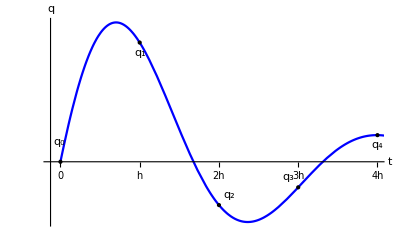

```mathematica
dibujito=Show[
Plot[σ[t],{t,0,tend},PlotStyle->Blue],
(*ListPlot[discretesigmas,PlotStyle->Red],*)
Epilog->{Directive[{Thick,Red,Dashed}],Black,PointSize[Large],Point[discretesigmas[[1]]],Text[Subscript[q, 0],Offset[{-1,20},discretesigmas[[1]]]],Directive[{Thick,Red,Dashed}],Black,PointSize[Large],Point[discretesigmas[[2]]],Text[Subscript[q, 1],Offset[{0,-10},discretesigmas[[2]]]],
Directive[{Thick,Red,Dashed}],Black,PointSize[Large],Point[discretesigmas[[3]]],Text[Subscript[q, 2],Offset[{10,10},discretesigmas[[3]]]],
Directive[{Thick,Red,Dashed}],Black,PointSize[Large],Point[discretesigmas[[4]]],Text[Subscript[q, 3],Offset[{-10,10},discretesigmas[[4]]]],
Directive[{Thick,Red,Dashed}],Black,PointSize[Large],Point[discretesigmas[[5]]],Text[Subscript[q, 4],Offset[{0,-10},discretesigmas[[5]]]]},
Ticks->{{{0,"0"},{2,"h"},{4,"2h"},{6,"3h"},{8,"4h"}},None},
AxesLabel->{"t","q"},
PlotRange->{{-.25,8},Automatic},
AxesOrigin->{-.25,0}
]
```

```mathematica
Export["./dibujo_discrete_continuous.pdf", dibujito]
```

./dibujo_discrete_continuous.pdf

### Discrete Euler-Lagrange equations

```mathematica
DEL:=D[Ldm[Q0,Q1],Q1]+D[Ldp[Q1,Q2],Q1]==0
```

```mathematica
solsDEL=FullSimplify[NSolve[{DEL,-π≤Q2<π},Q2]];
```

```mathematica
q2SolDEL[q0_,q1_]:=(solsDEL/.Q0->q0/.Q1->q1)[[1,1,2]]
```

```mathematica
q2SolDEL[0,1]
```

1.61719

### Runge-Kutta method

```mathematica
(*SolsRungeKutta=NDSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],{t,0,tend},
StartingStepSize->h,Method->{"FixedStep",Method->{"ExplicitRungeKutta"}}];*)
```

```mathematica
(*σRK[t_]=SolsRungeKutta[[1]][[1]][[2]]*)
```

```mathematica
RKsols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[Q[t]]],Q[0]==q0,Q'[0]==v0},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitRungeKutta","DifferenceOrder"->4}},StartingStepSize->h]][[-1,1]];
```

```mathematica
RKpts=Table[{h*n,RKsols[[n]]},{n,0,Floor[tend/h]}];
```

```mathematica
Eulersols=Reap[NDSolve[{ELeq,WhenEvent[Mod[t,h]==0,Sow[Q[t]]],Q[0]==q0,Q'[0]==v0},{},{t,tend},Method->{"FixedStep",Method->{"ExplicitEuler"}},StartingStepSize->h]][[-1,1]];
```

```mathematica
Eulerpts=Table[{h*n,Eulersols[[n]]},{n,0,Floor[tend/h]}];
```

```mathematica
(*SolsEuler=First@NDSolve[{ELeq,Q[0]==q0,Q'[0]==v0},Q[t],{t,0,tend},StartingStepSize->h,Method->{"FixedStep",Method->{"ExplicitEuler"
}}];*)
```

```mathematica
(*σEuler[t_]=SolsEuler[[1]][[2]]//Simplify;*)
```

### Continuous vs discrete

```mathematica
q1=σ[h];
```

```mathematica
qrecursive[0]=q0;
qrecursive[1]=q1;
qrecursive[n_]:=qrecursive[n]=q2SolDEL[qrecursive[n-2],qrecursive[n-1]]
```

```mathematica
(*qrecursiveminus[0]=q0;
qrecursiveminus[1]=q1;
qrecursiveminus[n_]:=qrecursiveminus[n]=q2SolDELminus[qrecursive[n-2],qrecursive[n-1]]*)
```

```mathematica
discretepts=Table[{h*n,qrecursive[n]},{n,0,Floor[tend/h]}];
```

```mathematica
(*discreteminuspts=Table[{h*n,qrecursiveminus[n]},{n,0,Floor[tend/h]}];*)
```

```mathematica
discretevels=Table[{(discretepts[[n+1,2]]+discretepts[[n,2]])/2,(discretepts[[n+1,2]]-discretepts[[n,2]])/h},{n,1,Floor[tend/h]}];
```

```mathematica
(*RKvels=Table[{(RKpts[[n+1,2]]+RKpts[[n,2]])/tendsmall2,(RKpts[[n+1,2]]-RKpts[[n,2]])/h},{n,1,Floor[tend/h]}];*)
```

```mathematica
(*Eulervels=Table[{(Eulerpts[[n+1,2]]+Eulerpts[[n,2]])/2,(Eulerpts[[n+1,2]]-Eulerpts[[n,2]])/h},{n,1,Floor[tend/h]}];*)
```

```mathematica
(*tendsmall=15;*)
```

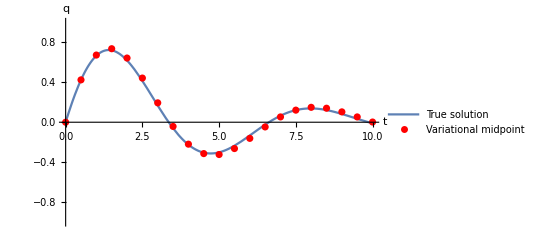

```mathematica
plot=Show[Plot[σ[t],{t,0,tend},PlotLegends->Placed[{"True solution"},Above]],ListPlot[Legended[discretepts,Placed["Variational midpoint",Above]],PlotStyle->Red],
(*ListPlot[Legended[discreteminuspts,Placed["Variational midpoint minus",Above]],PlotStyle->Purple],*)
(*ListPlot[Legended[RKpts,Placed["Runge-Kutta",Above]],PlotStyle->Orange],
ListPlot[Legended[Eulerpts, Placed["Euler method",Above]],PlotStyle->Green],*)
PlotRange->{{0,tend},{-1,1}}, 
AxesLabel->{"t","q"}]
```

```mathematica
discretevels=Table[{(discretepts[[n+1,2]]+discretepts[[n,2]])/2,(discretepts[[n+1,2]]-discretepts[[n,2]])/h},{n,1,100}];
```

Part::partw: Part 22 of {{0.,0},{0.5,0.424396},{1.,0.673121},{1.5,0.736623},«13»,{8.5,0.140309},{9.,0.103719},{9.5,0.0530369},{10.,0.00186792}} does not exist.

Part::partw: Part 23 of {{0.,0},{0.5,0.424396},{1.,0.673121},{1.5,0.736623},«13»,{8.5,0.140309},{9.,0.103719},{9.5,0.0530369},{10.,0.00186792}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
RKvels=Table[{RKpts[[n,2]],(2(RKpts[[n+1]][[2]]-RKpts[[n-1]][[2]]))/(3h)+(-RKpts[[n+2]][[2]]+RKpts[[n-2]][[2]])/(12h)},{n,4,100}];
```

Part::partw: Part 22 of {{0.,List},{0.5,0.424319},{1.,0.666419},{1.5,0.720829},«13»,{8.5,0.122357},{9.,0.0832408},{9.5,0.0347669},{10.,-0.0105245}} does not exist.

Part::partw: Part 23 of {{0.,List},{0.5,0.424319},{1.,0.666419},{1.5,0.720829},«13»,{8.5,0.122357},{9.,0.0832408},{9.5,0.0347669},{10.,-0.0105245}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

```mathematica
Eulervels=Table[{(Eulerpts[[n+1,2]]+Eulerpts[[n,2]])/2,(Eulerpts[[n+1,2]]-Eulerpts[[n,2]])/h},{n,1,100}];
```

Part::partw: Part 22 of {{0.,List},{0.5,0.5},{1.,0.875},{1.5,1.03639},{2.,0.965553},«12»,{8.5,0.815204},{9.,0.602072},{9.5,0.260257},{10.,-0.137692}} does not exist.

Part::partw: Part 23 of {{0.,List},{0.5,0.5},{1.,0.875},{1.5,1.03639},{2.,0.965553},«12»,{8.5,0.815204},{9.,0.602072},{9.5,0.260257},{10.,-0.137692}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Part::partw: Part 22 of {{0.,0.},{0.5,0.424396},{1.,0.673121},{1.5,0.736623},«13»,{8.5,0.140309},{9.,0.103719},{9.5,0.0530369},{10.,0.00186792}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

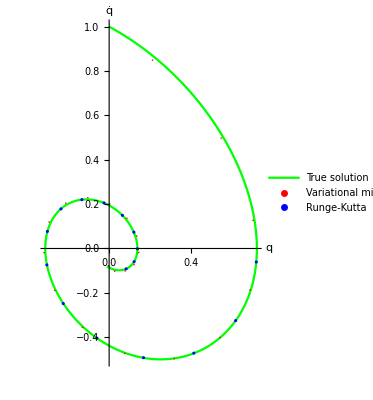

```mathematica
phasespace=Show[
ParametricPlot[{σ[t],σ'[t]},{t,0,tend},PlotStyle->Green,
PlotLegends->Placed[{"True solution"},Above]],
ListPlot[Legended[discretevels,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListPlot[Legended[RKvels,Placed["Runge-Kutta",Above]],PlotStyle->Blue],
(*ListPlot[Legended[Eulervels, Placed["Euler method",Above]],PlotStyle->Green],*)
(*PlotRange->{{-.3,10},{-.1,1}},*)
(*PlotRange->{{-.3,10},{-.3,5}},*)
AxesLabel->{"q","q̇"}
]
```

```mathematica
(*Export["./harmonic_oscillator_phase_space.pdf",phasespace];*)
```

```mathematica
(*Export["./harmonic_oscillator_plot.pdf",plot];*)
```

```mathematica
(*Conservedquantity[q_,v_]=Exp[r*q]*v;*)
```

```mathematica
(*Momenta[t_]=Conservedquantity[q,v]/.q->σ[t]/.v->σ'[t]*)
```

```mathematica
(*Momentapts=Table[{h*n,Conservedquantity[1/2(discretepts[[n]][[2]]+discretepts[[n-1]][[2]]),1/h(discretepts[[n]][[2]]-discretepts[[n-1]][[2]])]},{n,2,Floor[tend/h]}];*)
```

```mathematica
(*MomentaEulerpts=Table[{h*n,Conservedquantity[1/2(Eulerpts[[n]][[2]]+Eulerpts[[n-1]][[2]]),1/h(Eulerpts[[n]][[2]]-Eulerpts[[n-1]][[2]])]},{n,2,Floor[tend/h]}];*)
```

```mathematica
(*MomentaRKpts=Table[{h*n,Conservedquantity[1/2(RKpts[[n]][[2]]+RKpts[[n-1]][[2]]),1/h(RKpts[[n]][[2]]-RKpts[[n-1]][[2]])]},{n,2,Floor[tend/h]}];*)
```

```mathematica
(*momenta=Show[Plot[Momenta[t],{t,0,tendsmall},PlotLegends->Placed[{"True solution"},Above]],
ListPlot[Legended[Momentapts,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListPlot[Legended[MomentaEulerpts,Placed["Euler method",Above]],PlotStyle->Green],
ListPlot[Legended[MomentaRKpts,Placed["Runge-Kutta",Above]],PlotStyle->Orange],
PlotRange->{{0,tendsmall},{.9,1.1}},
AxesLabel->{"t","exp(rq) q̇"}]*)
```

```mathematica
(*Export["./harmonic_oscillator_momenta.pdf",momenta];*)
```

```mathematica
(*energypts=Table[{h*n,Hdmimp[qrecursive[n-2],qrecursive[n-1],qrecursive[n]]},{n,2,120}];*)
```

```mathematica
energypts=Table[{h*n,EL[(discretepts[[n]][[2]]+discretepts[[n-1]][[2]])/2,(discretepts[[n]][[2]]-discretepts[[n-1]][[2]])/h]},{n,2,Floor[tend/h]}];
```

```mathematica
energyRKpts=Table[{h*n,EL[(RKsols[[n]]+RKsols[[n-1]])/2,(RKsols[[n]]-RKsols[[n-1]])/h]},{n,2,Floor[tend/h]}];
```

```mathematica
energyEulerpts=Table[{h*n,EL[(Eulersols[[n]]+Eulersols[[n-1]])/2,(Eulersols[[n]]-Eulersols[[n-1]])/h]},{n,2,Floor[tend/h]}];;
```

```mathematica
(*energy=Show[Plot[Energy[t],{t,0,tend},PlotLegends->Placed[{"True solution"},Above]],ListPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green],
(*ListPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Orange],*)
(*PlotRange->{{0,tend},Automatic},*)
 AxesLabel->{"t","E_L"}]*)
```

```mathematica
(*energylog=Show[LogPlot[Energy[t],{t,0,tend},
PlotLegends->Placed[{"True solution"},Above]],
ListLogPlot[Legended[energypts,Placed["Variational midpoint",Above]],PlotStyle->Red],
ListLogPlot[Legended[energyEulerpts, Placed["Euler method",Above]],PlotStyle->Green],
ListLogPlot[Legended[energyRKpts, Placed["Runge-Kutta",Above]],PlotStyle->Orange],
(*PlotRange->{{0,10},Automatic}, *)
(*PlotRange->{{0,100},{-50,0}},*)
AxesLabel->{"t","log E_L"}]
*)
```

```mathematica
(*Export["./harmonic_oscillator_energy.pdf",energy];*)
```

```mathematica
(*Export["./harmonic_oscillator_energy_log.pdf",energylog];*)
```

```mathematica
AbsoluteTime[]-tstart
```

3.755823